```mathematica
f[x_]:=π^2 x
```

```mathematica
L=π
```

π

```mathematica
a0=1/(2*L)∫_-L^L (f[x])ⅆx
```

0

```mathematica
a[n_]:=1/L∫_-L^L (f[x]*Cos[(n*x*π)/L])ⅆx
```

```mathematica
b[n_]:=1/L∫_-L^L (f[x]*Sin[(n*x*π)/L])ⅆx
```

```mathematica
sf=a0+∑_(n=0)^10 ((a[n]*Cos[(n*x*π)/L])+(b[n]*Sin[(n*x*π)/L]))
```

2 π^2 Sin[x]-π^2 Sin[2 x]+2/3 π^2 Sin[3 x]-1/2 π^2 Sin[4 x]+2/5 π^2 Sin[5 x]-1/3 π^2 Sin[6 x]+2/7 π^2 Sin[7 x]-1/4 π^2 Sin[8 x]+2/9 π^2 Sin[9 x]-1/5 π^2 Sin[10 x]

```mathematica
∫sfⅆx
```

π^2 x-4 Sin[x]+1/2 Sin[2 x]-4/27 Sin[3 x]+1/16 Sin[4 x]-4/125 Sin[5 x]+1/54 Sin[6 x]-4/343 Sin[7 x]+1/128 Sin[8 x]-4/729 Sin[9 x]+1/250 Sin[10 x]

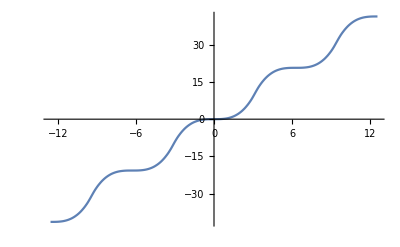

```mathematica
Plot[{(π^2 x)/3-4 Sin[x]+1/2 Sin[2 x]-4/27 Sin[3 x]+1/16 Sin[4 x]-4/125 Sin[5 x]+1/54 Sin[6 x]-4/343 Sin[7 x]+1/128 Sin[8 x]-4/729 Sin[9 x]+1/250 Sin[10 x]},{x,-4π,4π}]
```

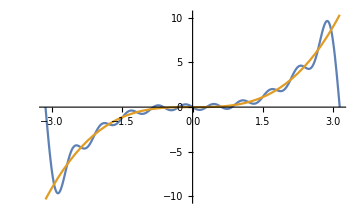

```mathematica
Show[%74,ImageSize->Medium]
```

```mathematica
D[sf, x]
```

4 Sin[x]-2 Sin[2 x]+4/3 Sin[3 x]-Sin[4 x]+4/5 Sin[5 x]-2/3 Sin[6 x]+4/7 Sin[7 x]-1/2 Sin[8 x]+4/9 Sin[9 x]-2/5 Sin[10 x]

```mathematica
∫(4 Sin[x]-2 Sin[2 x]+4/3 Sin[3 x]-Sin[4 x]+4/5 Sin[5 x]-2/3 Sin[6 x]+4/7 Sin[7 x]-1/2 Sin[8 x]+4/9 Sin[9 x]-2/5 Sin[10 x])ⅆx
```

-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x]

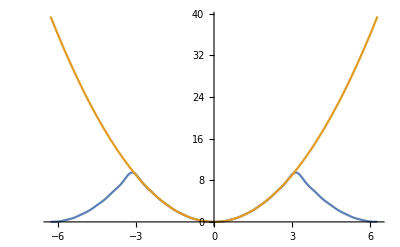

```mathematica
Plot[{π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x],x^2},{x,-2π,2π}]
```

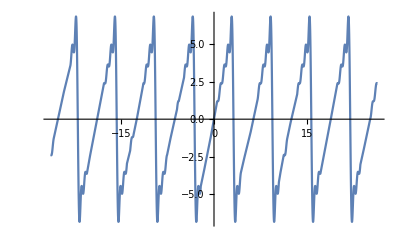

```mathematica
Plot[4 Sin[x]-2 Sin[2 x]+4/3 Sin[3 x]-Sin[4 x]+4/5 Sin[5 x]-2/3 Sin[6 x]+4/7 Sin[7 x]-1/2 Sin[8 x]+4/9 Sin[9 x]-2/5 Sin[10 x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
a[n]
```

(4 n π Cos[n π]+2 (-2+n^2 π^2) Sin[n π])/(n^3 π)

```mathematica
a[1]
```

-4

```mathematica
a[2]
```

1

```mathematica
a[3]
```

-4/9

```mathematica
nf=4 Sin[x]-2 Sin[2 x]+4/3 Sin[3 x]-Sin[4 x]+4/5 Sin[5 x]-2/3 Sin[6 x]+4/7 Sin[7 x]-1/2 Sin[8 x]+4/9 Sin[9 x]-2/5 Sin[10 x]
```

4 Sin[x]-2 Sin[2 x]+4/3 Sin[3 x]-Sin[4 x]+4/5 Sin[5 x]-2/3 Sin[6 x]+4/7 Sin[7 x]-1/2 Sin[8 x]+4/9 Sin[9 x]-2/5 Sin[10 x]

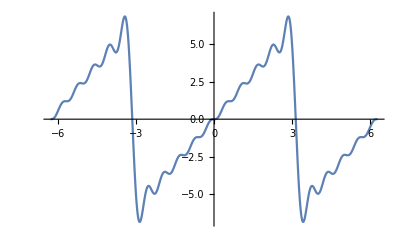

```mathematica
Plot[nf,{x,-2π,2π}]
```

```mathematica
D[nf, x]
```

4 Cos[x]-4 Cos[2 x]+4 Cos[3 x]-4 Cos[4 x]+4 Cos[5 x]-4 Cos[6 x]+4 Cos[7 x]-4 Cos[8 x]+4 Cos[9 x]-4 Cos[10 x]

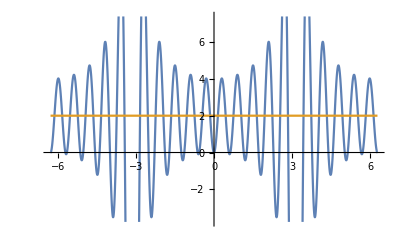

```mathematica
Plot[{4 Cos[x]-4 Cos[2 x]+4 Cos[3 x]-4 Cos[4 x]+4 Cos[5 x]-4 Cos[6 x]+4 Cos[7 x]-4 Cos[8 x]+4 Cos[9 x]-4 Cos[10 x],2},{x,-2π,2π}]
```